```mathematica
z = PauliMatrix[3]
x = PauliMatrix[1]
I1 = IdentityMatrix[2]
I2 = IdentityMatrix[2^2]
I3 = IdentityMatrix[2^3]
```

{{1,0},{0,-1}}

{{0,1},{1,0}}

{{1,0},{0,1}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
H=-2m (KroneckerProduct[I2,z, I1] + KroneckerProduct[I3,z]) - KroneckerProduct[z,I1,z,I1] -KroneckerProduct[I1,z,I1,z] - Δ(KroneckerProduct[x,I3] + KroneckerProduct[I1,x,I2] + τ (KroneckerProduct[x,x,I2] + KroneckerProduct[I2,x,x]) + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]) //MatrixForm
```

(-2-4 m | -Δ | -Δ | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0
-Δ | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0
-Δ | -Δ τ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0
-Δ τ | -Δ | -Δ | 2+4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ τ | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | -2 | -Δ τ | -Δ | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | -Δ τ | 2 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ τ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ τ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 2 | -Δ τ | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | -Δ | -Δ τ | -2 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | -Δ τ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
-Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 2-4 m | -Δ | -Δ | -Δ τ
0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ τ | -Δ
0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | -Δ
0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | -Δ | -Δ | -2+4 m)

```mathematica
({{-4 m, -Δ, -Δ, -Δ τ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ τ, 0, 0, 0}, {-Δ, -2, -Δ τ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ τ, 0, 0}, {-Δ, -Δ τ, -2-4 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ τ, 0}, {-Δ τ, -Δ, -Δ, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ τ}, {-Δ, 0, 0, 0, 2-4 m, -Δ, -Δ, -Δ τ, -Δ τ, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, 0, -Δ τ, -Δ, 0, -Δ τ, 0, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, -Δ τ, -4 m, -Δ, 0, 0, -Δ τ, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ τ, -Δ, -Δ, 2, 0, 0, 0, -Δ τ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ τ, 0, 0, 0, 2, -Δ, -Δ, -Δ τ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, -Δ τ, 0, 0, -Δ, 4 m, -Δ τ, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, 0, -Δ τ, 0, -Δ, -Δ τ, 0, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, -Δ τ, -Δ τ, -Δ, -Δ, 2+4 m, 0, 0, 0, -Δ}, {-Δ τ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, -Δ, -Δ, -Δ τ}, {0, -Δ τ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, -2+4 m, -Δ τ, -Δ}, {0, 0, -Δ τ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ τ, -2, -Δ}, {0, 0, 0, -Δ τ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ τ, -Δ, -Δ, 4 m}})
Ham = Ham = H/. τ->1 //MatrixForm
```

{{-4 m,-Δ,-Δ,-Δ τ,-Δ,0,0,0,-Δ,0,0,0,-Δ τ,0,0,0},{-Δ,-2,-Δ τ,-Δ,0,-Δ,0,0,0,-Δ,0,0,0,-Δ τ,0,0},{-Δ,-Δ τ,-2-4 m,-Δ,0,0,-Δ,0,0,0,-Δ,0,0,0,-Δ τ,0},{-Δ τ,-Δ,-Δ,0,0,0,0,-Δ,0,0,0,-Δ,0,0,0,-Δ τ},{-Δ,0,0,0,2-4 m,-Δ,-Δ,-Δ τ,-Δ τ,0,0,0,-Δ,0,0,0},{0,-Δ,0,0,-Δ,0,-Δ τ,-Δ,0,-Δ τ,0,0,0,-Δ,0,0},{0,0,-Δ,0,-Δ,-Δ τ,-4 m,-Δ,0,0,-Δ τ,0,0,0,-Δ,0},{0,0,0,-Δ,-Δ τ,-Δ,-Δ,2,0,0,0,-Δ τ,0,0,0,-Δ},{-Δ,0,0,0,-Δ τ,0,0,0,2,-Δ,-Δ,-Δ τ,-Δ,0,0,0},{0,-Δ,0,0,0,-Δ τ,0,0,-Δ,4 m,-Δ τ,-Δ,0,-Δ,0,0},{0,0,-Δ,0,0,0,-Δ τ,0,-Δ,-Δ τ,0,-Δ,0,0,-Δ,0},{0,0,0,-Δ,0,0,0,-Δ τ,-Δ τ,-Δ,-Δ,2+4 m,0,0,0,-Δ},{-Δ τ,0,0,0,-Δ,0,0,0,-Δ,0,0,0,0,-Δ,-Δ,-Δ τ},{0,-Δ τ,0,0,0,-Δ,0,0,0,-Δ,0,0,-Δ,-2+4 m,-Δ τ,-Δ},{0,0,-Δ τ,0,0,0,-Δ,0,0,0,-Δ,0,-Δ,-Δ τ,-2,-Δ},{0,0,0,-Δ τ,0,0,0,-Δ,0,0,0,-Δ,-Δ τ,-Δ,-Δ,4 m}}

(-2-4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
-Δ | 0 | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0
-Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0
-Δ | -Δ | -Δ | 2+4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | -2 | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | -Δ | 2 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 2 | -Δ | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | -2 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 2-4 m | -Δ | -Δ | -Δ
0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ
0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 0 | -Δ
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | -2+4 m)

```mathematica
eg = Eigenvalues[Ham]
```

```mathematica
Eigenvalues[({{-2-4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {-Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {-Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {-Δ, -Δ, -Δ, 2+4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, -2, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, -Δ, 2, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ, -Δ, -Δ, 4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, -4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 2, -Δ, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, -2, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, 4 m, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 2-4 m, -Δ, -Δ, -Δ}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, -2+4 m}})]
```

{2 Δ,Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,1],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,2],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,3],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,4],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,2],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,3],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,4],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,6],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,7],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,8],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,9],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,10]}

```mathematica
ds = Range[1.08,1.11,0.001];
```

```mathematica
Table[Plot[{Table[Plot[{Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1]}+2 m^2,{m,-0.6,0.6}, PlotLegends->"Expressions"],{Δ,ds}]}+2 m^2,{m,-0.6,0.6}, PlotLegends->"Expressions"],{Δ,ds}]
```

```mathematica
Eigenvalues[({{-4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {-Δ, -2, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {-Δ, -Δ, 2, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {-Δ, -Δ, -Δ, 4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -2-4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ, -Δ, -Δ, 2+4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, 2-4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, -2+4 m, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -4 m, -Δ, -Δ, -Δ}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 2, -Δ, -Δ}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, -2, -Δ}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, 4 m}})]
```

{2 Δ,Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,1],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,2],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,3],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,4],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,2],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,3],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,4],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,6],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,7],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,8],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,9],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,10]}

```mathematica
ds = Range[0.1,1.1,0.1];
```

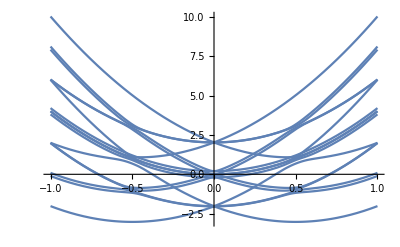
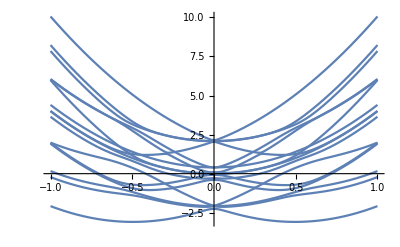
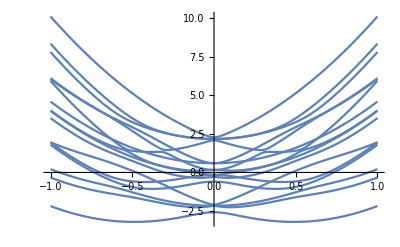
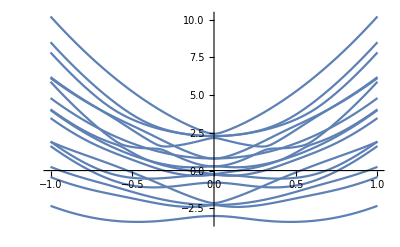
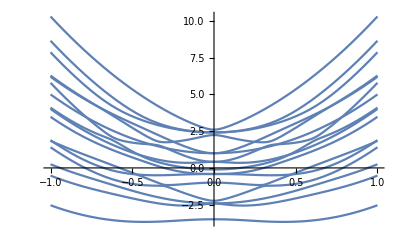
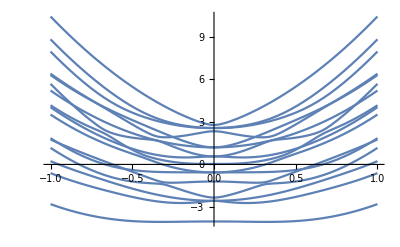
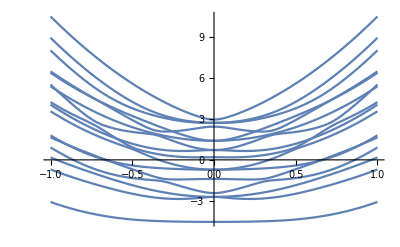
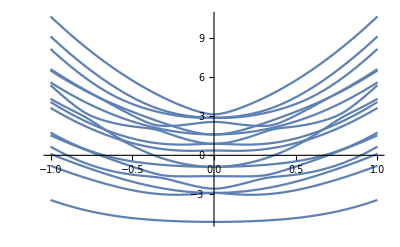

```mathematica
Table[Plot[{2 Δ,Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,1],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,2],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,3],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,4],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,2],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,3],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,4],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,6],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,7],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,8],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,9],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,10]}+4 m^2,{m,-1,1}],{Δ,ds}]
```

```mathematica
ds = Range[1.08,1.11,0.001];
```

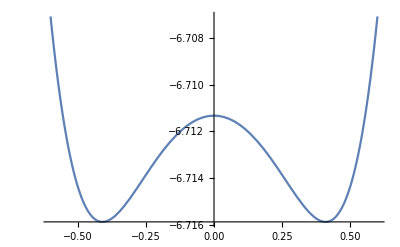
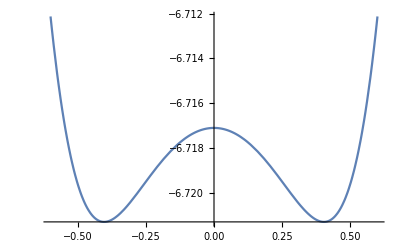
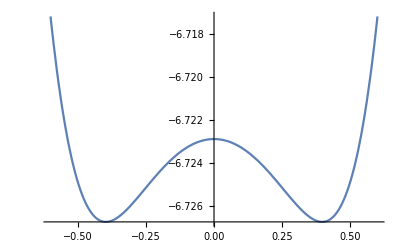
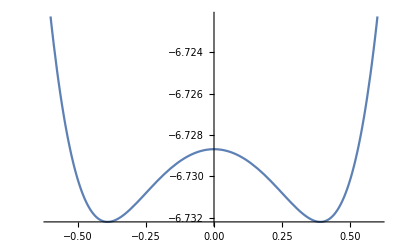
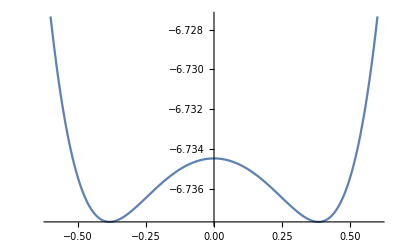
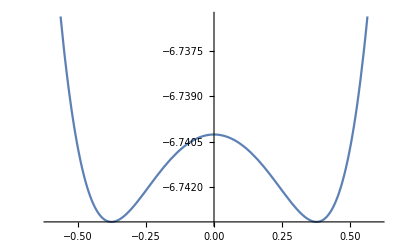
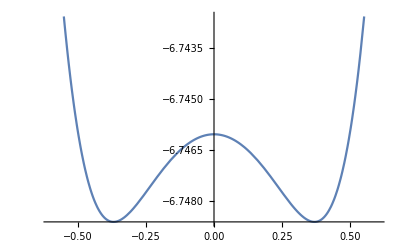
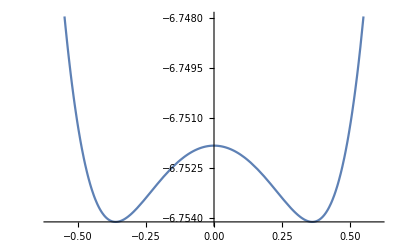

```mathematica
Table[Plot[{Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1]}+2 m^2,{m,-0.6,0.6}, PlotLegends->"Expressions"],{Δ,ds}](*3ladder 2rung - 2nd order*)
```

```mathematica
Series[{Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1]}+2 m^2/.{Δ->1.3},{m,0,6}]
```

Series::icm: Series in m to be combined have unequal expansion points 0 and 0..

{(2 m^2+O[m]^7)+(-7.99224-1.64781 (m+0.)^2+0.0121617 (m+0.)^4+0.181046 (m+0.)^6+O[m+0.]^7)}

```mathematica
{AlgebraicNumber"-6.25"AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{0,1,0}]-6.249770839529148+AlgebraicNumber"-0.244"AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{-8870/781,4786/781,988/781}]-0.24389669387602497 m^2+AlgebraicNumber"0.0435"AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{2853888630/6709571,-1994469155/6709571,-1568736809/26838284}]0.04348835848865487 m^4+O[m]^5}
```

{AlgebraicNumber-6.25AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{0,1,0}]-6.249770839529148+AlgebraicNumber-0.244AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{-8870/781,4786/781,988/781}]-0.24389669387602497 m^2+AlgebraicNumber0.0435AlgebraicNumber[Root[16-24 #1+2 #1^2+#1^3&,1],{2853888630/6709571,-1994469155/6709571,-1568736809/26838284}]0.04348835848865487 m^4+O[m]^5}

```mathematica
{(2 m^2+O[m]^5)+(-6.307306439077021-2.216757287563701 (m+0.)^2+0.041439017274618586 (m+0.)^4+O[m+0.]^5)}
```

```mathematica
{Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(2+(-8192 Δ^4-155648 Δ^6+524288 Δ^8+(-114688 Δ^5-524288 Δ^7) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(4096 Δ^2+30720 Δ^4+131072 Δ^6) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2)/(4096 Δ^5+77824 Δ^7-262144 Δ^9+(3072 Δ^4+36864 Δ^6+262144 Δ^8) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-5120 Δ^5-65536 Δ^7) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2)) m^2+((-131072 Δ^4+2482176 Δ^6+80830464 Δ^8+513343488 Δ^10+1036386304 Δ^12+1700790272 Δ^14+36238786560 Δ^16-214748364800 Δ^18+(-131072 Δ^3-917504 Δ^5+35454976 Δ^7+546275328 Δ^9+3464101888 Δ^11+14321451008 Δ^13+57713623040 Δ^15+214748364800 Δ^17) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-32768 Δ^2-1081344 Δ^4-13973504 Δ^6-114335744 Δ^8-693796864 Δ^10-2888302592 Δ^12-11072962560 Δ^14-53687091200 Δ^16) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2) m^4)/(221184 Δ^9+14000128 Δ^11+389070848 Δ^13+5957484544 Δ^15+53670313984 Δ^17+239444426752 Δ^19+68719476736 Δ^21-4398046511104 Δ^23+(110592 Δ^8+6893568 Δ^10+215728128 Δ^12+4019716096 Δ^14+48536485888 Δ^16+383325831168 Δ^18+1855425871872 Δ^20+4398046511104 Δ^22) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-497664 Δ^9-23072768 Δ^11-540147712 Δ^13-7755268096 Δ^15-71135395840 Δ^17-395136991232 Δ^19-1099511627776 Δ^21) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2)+((931135488 Δ^4+90133495808 Δ^6+4631411294208 Δ^8+165118643011584 Δ^10+4434669801963520 Δ^12+93401088999948288 Δ^14+1581458495675564032 Δ^16+21841609970653593600 Δ^18+247658255001757679616 Δ^20+2304491198904352636928 Δ^22+17461496830157178011648 Δ^24+105848075877835195023360 Δ^26+495428083525546175102976 Δ^28+1653053487407078670598144 Δ^30+2983252721783763015565312 Δ^32-3683986000363231574491136 Δ^34-45927116974731702592077824 Δ^36-161155478594409512562589696 Δ^38-315982986101773700538826752 Δ^40-309485009821345068724781056 Δ^42+(427819008 Δ^3+44084232192 Δ^5+2373183340544 Δ^7+88907409522688 Δ^9+2536490761977856 Δ^11+57395273150234624 Δ^13+1056379728957538304 Δ^15+16079104792224858112 Δ^17+204460862556612853760 Δ^19+2183400619178459136000 Δ^21+19604522527018482401280 Δ^23+147653141767314944819200 Δ^25+927294329644772749213696 Δ^27+4808915882370878289215488 Δ^29+20302606953778768395632640 Δ^31+68395300255673882251362304 Δ^33+178617941297834069923463168 Δ^35+345337216159291415187161088 Δ^37+451382677898612168105918464 Δ^39+309485009821345068724781056 Δ^41) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-18874368 Δ^2-2504523776 Δ^4-178409439232 Δ^6-8156977299456 Δ^8-267405538492416 Δ^10-6736735657492480 Δ^12-135661295340814336 Δ^14-2233588095978831872 Δ^16-30468140998072991744 Δ^18-346811186395155005440 Δ^20-3302415956418054062080 Δ^22-26266645154852054761472 Δ^24-173572143216743369670656 Δ^26-943976629438739090767872 Δ^28-4166052002534911708758016 Δ^30-14624795594994986684252160 Δ^32-39685227618906343628341248 Δ^34-79583681152560695963811840 Δ^36-108009966196194525327654912 Δ^38-77371252455336267181195264 Δ^40) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2) m^6)/(143327232 Δ^13+37265080320 Δ^15+3359339053056 Δ^17+176366490681344 Δ^19+6374924459835392 Δ^21+171567603163070464 Δ^23+3586955388555100160 Δ^25+59653014594795864064 Δ^27+798373945125288017920 Δ^29+8616197416789894758400 Δ^31+74386112530527952044032 Δ^33+502621237015332377329664 Δ^35+2532721243958504637595648 Δ^37+8414039587364842940399616 Δ^39+9966554462096386223505408 Δ^41-59690712343472315501117440 Δ^43-338499229492096168917729280 Δ^45-618970019642690137449562112 Δ^47+(71663616 Δ^12+17796464640 Δ^14+1641637380096 Δ^16+89774546583552 Δ^18+3419529727574016 Δ^20+98021493048344576 Δ^22+2208041680509075456 Δ^24+40107191533955973120 Δ^26+596450360917481226240 Δ^28+7319178386661980504064 Δ^30+74247209977545800810496 Δ^32+620207250910221963362304 Δ^34+4222243545690002581094400 Δ^36+22988664506050169995788288 Δ^38+96957267443038120704999424 Δ^40+299662487536976206680293376 Δ^42+609298613085773104051912704 Δ^44+618970019642690137449562112 Δ^46) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-704692224 Δ^13-100330389504 Δ^15-7001241108480 Δ^17-316391645544448 Δ^19-10354954373955584 Δ^21-260159613708533760 Δ^23-5189365630909808640 Δ^25-83830459589401247744 Δ^27-1108686446478883815424 Δ^29-12051381280873616769024 Δ^31-107416185626544949952512 Δ^33-777957564239502513274880 Δ^35-4497546789471310053376000 Δ^37-20123774470938634372513792 Δ^39-65999793964586161506615296 Δ^41-142653246714526242615328768 Δ^43-154742504910672534362390528 Δ^45) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2)+((-2900704679165952 Δ^3-2144133268566441984 Δ^5-536639340746517774336 Δ^7-78236286468625715429376 Δ^9-7971940125649517099876352 Δ^11-621144892205374383870443520 Δ^13-39021902694170841240569905152 Δ^15-2046250633726785679375311306752 Δ^17-91763990226496606983607591895040 Δ^19-3582368392366711629592153865060352 Δ^21-123399355670577501482175218039128064 Δ^23-3790202321334488054511725697564672000 Δ^25-104673863275506935874745990498788311040 Δ^27-2616688114390172242380443932249865322496 Δ^29-59534343941100772735483020938397089792000 Δ^31-1238268353720739971042967947791936834764800 Δ^33-23630357615104693865054925768843375237136384 Δ^35-414970715519452692613534752515987154346704896 Δ^37-6721870256612312913215470775192514220640960512 Δ^39-100624860308631737446084270339823797040899424256 Δ^41-1394077000325383669974067795567086259173240864768 Δ^43-17892952734367955964057605266882684880243075842048 Δ^45-212898769043876608676874623104792949196310049718272 Δ^47-2348998029170945882226974252611906421129418534551552 Δ^49-24031123653722072140910280976422365156178421023244288 Δ^51-227849137376045371034748824576812947147108752994336768 Δ^53-2000451532512498845780005311865348164354849957635686400 Δ^55-16242321207864653746756823094642517933690864514747072512 Δ^57-121735292002933214839337184130892120140369802170172702720 Δ^59-840181495938926714453418551954163574822217564083202293760 Δ^61-5322520923246572879119311495105555952452869634299151777792 Δ^63-30817279239062414509865275139345792726600783141505628897280 Δ^65-162144940668566850762014417840354303746382215104104518123520 Δ^67-769055061317031408786482338904702275082986094492982079127552 Δ^69-3249498348464175697390351479938895222280516527075645930340352 Δ^71-12001120720950966942369789011507501716062977429754527170428928 Δ^73-37407706542911962742099714502681756009505424577334892229033984 Δ^75-90692576716764440632660386913436836526292489116913536247791616 Δ^77-124245530883553407707895980717428815490175563978911153410539520 Δ^79+227774853766610981719772003071436286838130862131401277862576128 Δ^81+2396410887625578057260844073662273813639419143775151291889614848 Δ^83+10309477756050825752226205549132642902011521951226232966637158400 Δ^85+31639843426874243708296314464625374276485493214719100690840420352 Δ^87+75488187443893749174289376136098692982781047448230418226907971584 Δ^89+141812196389946174095968312711805659780030556048742017794123497472 Δ^91+205661725453805054293540424490933288447851903631191497923729817600 Δ^93+218614429943611722326169022949407282081524570542716935622568706048 Δ^95+152604478311099270507117972061270847711123529507576704397230473216 Δ^97+52656145834278593348959013841835216159447547700274555627155488768 Δ^99+(-1450352339582976 Δ^2-1035633466495991808 Δ^4-258577986576030105600 Δ^6-37925173020744430387200 Δ^8-3904760942782414640381952 Δ^10-308328283622061591326883840 Δ^12-19674378959883555918974025728 Δ^14-1049892693133046285698452160512 Δ^16-47993491896900185006567516536832 Δ^18-1912866422620871277628346467352576 Δ^20-67373341385589763313449214196842496 Δ^22-2119089435906933416095986644270710784 Δ^24-60020025587412868881614513444902404096 Δ^26-1541204316519522895386464118506151477248 Δ^28-36077440974322177641001896455544485445632 Δ^30-773379208325943078783084065312672166445056 Δ^32-15239030183148728048255665274330985739059200 Δ^34-276868955701887831113277028619885744545071104 Δ^36-4649964591005166152405577994554939273855893504 Δ^38-72341302233847685294923380630589645006691106816 Δ^40-1044262417229927413310278606505285104983328423936 Δ^42-14005135218083115031655441753914868388050937839616 Δ^44-174680435565021209704549787646405938010046678958080 Δ^46-2027560562591116834166342344673424539789139202015232 Δ^48-21910155727434088577087457042739986000958221413515264 Δ^50-220449822678717761722709348877972445961204650989322240 Δ^52-2064909130007040175147585766513732398654435372998590464 Δ^54-17998529905360359263076389729458899766069175938963210240 Δ^56-145887317097349871971808601000250854780823750580388233216 Δ^58-1098547359634165613536208620992330835352925310284667551744 Δ^60-7675143457097207699291147107219832481549104221840753033216 Δ^62-49673557650452093539422210404648013916624348488122981416960 Δ^64-297224213099404253850044963023234790686623898720104628617216 Δ^66-1640355106317896788877458277803650451744683936299713529118720 Δ^68-8326477618479996899250577533582079207346939503594166160457728 Δ^70-38743300677197074726381930067943342677641152851045062681821184 Δ^72-164591930745488784278697008653338882555743075940861200794910720 Δ^74-635366451432429052624532852357107132157763362843618956579700736 Δ^76-2215900036603762854870709814095647967033412004025237018450591744 Δ^78-6933519637076438965034554212038709662395077202108651623147372544 Δ^80-19297100469675494430656194220074409135469359594112775051607539712 Δ^82-47255545542227833981319948340342610072139294961601768670109892608 Δ^84-100403360153131940796988825952034075141898060928787846611869892608 Δ^86-181654416127547663457004733831119811924241876667806242311736655872 Δ^88-272641741614500596450545744963209857306444749571710498789572739072 Δ^90-326557791559050027042966590674551866906519726598851633125085151232 Δ^92-293195035851993381873269239343360692853809110064041248147262930944 Δ^94-175641542113596155097287540617073754780881831626446822484110999552 Δ^96-52656145834278593348959013841835216159447547700274555627155488768 Δ^98) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(24017993251946496 Δ^3+9374458019196174336 Δ^5+1761143942795287855104 Δ^7+215159787860342486335488 Δ^9+19357086305930938134036480 Δ^11+1372406894967636354689662976 Δ^13+80001947930368120675708698624 Δ^15+3946388433508570207074998288384 Δ^17+168177612696378446554862056374272 Δ^19+6288244905087020315618881019248640 Δ^21+208769121898652886513616574556405760 Δ^23+6212468632931937799117914524595257344 Δ^25+166954894002379671850565126553306398720 Δ^27+4076908333412503846070730280655905619968 Δ^29+90915577415230612497214259329310945968128 Δ^31+1859153709537182122788554864037295971893248 Δ^33+34981780521145792453270062462327424244776960 Δ^35+607346376258438608819941933089511709960306688 Δ^37+9752029316747613162802339377365645968699031552 Δ^39+145084628514264009212421688770620369706514644992 Δ^41+2002857137407203017136213921449786178898768166912 Δ^43+25684002860496809146568263556631345584172167069696 Δ^45+306197809072508130705798083831180192595456085196800 Δ^47+3395315742583849590074234960985616652245988483792896 Δ^49+35025533346604695546061439931925769817138526855102464 Δ^51+336110957002682808666660362501126211019390902524182528 Δ^53+2999304578571535220655324711304326819859734115360178176 Δ^55+24872720189193988534144273944955361256243849088877985792 Δ^57+191509164034596361506609649438796256767935078577473585152 Δ^59+1367366837508043480210580467380026140581542801857581154304 Δ^61+9039242912721794832408692137623608309013111285486991704064 Δ^63+55219897674315504650042744807210306473396858812453066113024 Δ^65+311002999826680161416007677726753552250034414102653266034688 Δ^67+1610374918388661645265674766176954722299333405510280467709952 Δ^69+7640767687117822771337725840324731146130976583654914790522880 Δ^71+33088020586425982877409768931069170231089277214315646378049536 Δ^73+130156808217919599711693487882528980821305340014207760364208128 Δ^75+462427285522915076481690586681769134392889018928526127483846656 Δ^77+1473605239656364960061041623221742460161988342735356041917104128 Δ^79+4175923578942037780387311864575501416089492374682098833213620224 Δ^81+10410331885615735316734344307333286483738103359899800297116008448 Δ^83+22514085066202591166380092381640898246869226562379562671155445760 Δ^85+41459230936877208100852576256059336605592735711715636630612082688 Δ^87+63336303172802917098089986805129671755612574462381459143401668608 Δ^89+77227389990979030428770697724643305245538585914169291564799492096 Δ^91+70605781884889693233739534800653312998281709392648129806231142400 Δ^93+43087633249738435753244400562989763442729089973794915689353445376 Δ^95+13164036458569648337239753460458804039861886925068638906788872192 Δ^97) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2) m^8)/(79623006028038144 Δ^18+47258330414532526080 Δ^20+11863685383228118532096 Δ^22+1814056507228397707984896 Δ^24+196158777282078861296664576 Δ^26+16253972062093488584619196416 Δ^28+1084533136006497486751181832192 Δ^30+60247795730727463516747811782656 Δ^32+2853456255427549013869796117184512 Δ^34+117270706264758823076582171388936192 Δ^36+4238894379276931092648007446495756288 Δ^38+136188881194804719467354155193588514816 Δ^40+3921931470311085816032509508678911524864 Δ^42+101919794852643239661296155116873946497024 Δ^44+2403209196213188408174184350528499483672576 Δ^46+51644858894795265421099113757027325001596928 Δ^48+1015140630616674144551530500911136224619528192 Δ^50+18303788958907020144247602329987121389666041856 Δ^52+303428671968711679662900082942889282311781613568 Δ^54+4632565141509401323884747898265400151529316417536 Δ^56+65218138478795176299631750287626548837059483664384 Δ^58+847280061006710504233239835260679787146232396251136 Δ^60+10160850901615107842524909836855517220024920542543872 Δ^62+112463692811825396389106740923339543236257181081796608 Δ^64+1148157959596467838863205094294448463252749545356918784 Δ^66+10799443485425574168068094701495053877438034606508998656 Δ^68+93424554766073266841732049881523430149615797992947712000 Δ^70+741532560452860171969792665482159559960532473102158790656 Δ^72+5382543840210330301002222392587458302768018538681698615296 Δ^74+35573693520053822518969445576862002508062294883406092173312 Δ^76+212806430174350546492214402829840449540537913769472328466432 Δ^78+1142886359332899959352665314950091264984753476559327329255424 Δ^80+5445701028876628539338749310331030305092532979729179122597888 Δ^82+22603374296214450262974743868934718794255420797093510406733824 Δ^84+79150642212977891506950524679524042531145542428150843593195520 Δ^86+218337599277606341920695127377715898792101055375362392925929472 Δ^88+379464045365600126900215116120738363881712359510829651472678912 Δ^90-226217490653393029976409580985947066556437128938870595433529344 Δ^92-4978619765456643182719843178283296052125197732602208129101332480 Δ^94-22964983058631722411623346706382535535343896758506907020564627456 Δ^96-68913060968314908578878992810054594426517051609361291475276529664 Δ^98-148407156139494787907402367076075730993335535287816049511423279104 Δ^100-225665523431378522374908820551654146597398010822905163447042834432 Δ^102-220497610681041609648765870462684967667686605994899701688713609216 Δ^104-105312291668557186697918027683670432318895095400549111254310977536 Δ^106+(38999023360671744 Δ^17+22822372911492366336 Δ^19+5720749644612378820608 Δ^21+879018626877980204335104 Δ^23+95902719379491181679345664 Δ^25+8041588197472632429632028672 Δ^27+544260819562903091413184937984 Δ^29+30729747099892348325259934433280 Δ^31+1481921062471505255556889983320064 Δ^33+62117112453694216253103896763826176 Δ^35+2293768322373070798575744275548471296 Δ^37+75407736657219405941088358310785056768 Δ^39+2225683934128777008023759088086817964032 Δ^41+59380805969106338528863598952287702089728 Δ^43+1440034438706241365519221371405530403176448 Δ^45+31887359071512486610594805957877917206708224 Δ^47+647147501615154736013630378160010674328043520 Δ^49+12074014627028421970897323661135705631203786752 Δ^51+207604548013376410271156280607702505090545876992 Δ^53+3296196493209379574006314128891833343273164865536 Δ^55+48399444344070086438280083759119762228360094154752 Δ^57+657964043924468469466820655727771693417947715338240 Δ^59+8287389512611735405662961519755067337296098914992128 Δ^61+96749805504074939834205417151955921385096578192113664 Δ^63+1046910371596688990581778328703866770822085295762046976 Δ^65+10496714318510201249982307570793699836232899650184544256 Δ^67+97450064598434473968914361968636865592845614903201890304 Δ^69+836817585988412822057671265924220761709759409525566210048 Δ^71+6636756913761718402072843797250214239437900776833873346560 Δ^73+48519539288440209815314974057089639502032212043990302720000 Δ^75+326173752000142919295690178522116031876425265451858997018624 Δ^77+2010159410005226754156407786427769554912375066394957229064192 Δ^79+11314436720076985633827615067871209626640676377477264980312064 Δ^81+57897260891465723680923911261513727861436009717542896214736896 Δ^83+267823608043121046417709052876255571772982879658806886977765376 Δ^85+1112156828206232744899537662371759022848884519911679032272355328 Δ^87+4109693937664682841452646599398530951163524738157346229552414720 Δ^89+13364547502370998795342150766176805574460831143188666776895356928 Δ^91+37700087682721692346999221417295780936718079949141554399606210560 Δ^93+90493754781241806281653632874937143287117895921700544964712202240 Δ^95+179959510180554769701284069474982922847187313117850076113256054784 Δ^97+285065988237412097910317449295045222199631244488086100603958198272 Δ^99+337765521398885683996716096113373649749346891669192791637666824192 Δ^101+266571738286035378829105007574290781807203210232639937862474661888 Δ^103+105312291668557186697918027683670432318895095400549111254310977536 Δ^105) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]+(-406239826673664 Δ^16-565892078556413952 Δ^18-205214305332127334400 Δ^20-39733856674025035530240 Δ^22-5122671939647462417891328 Δ^24-489245768732302387779207168 Δ^26-36831978415984513007090663424 Δ^28-2275469393605850731874762096640 Δ^30-118633770007523059660776400748544 Δ^32-5327116715031104676968101866110976 Δ^34-209224560571546573202766102314090496 Δ^36-7273768548857370881953799942719930368 Δ^38-225964183946726265660527759110302597120 Δ^40-6320501308449902326086644483332321050624 Δ^42-160166716735530330411189317310678011215872 Δ^44-3695632668594601403562472369355294848843776 Δ^46-77963682593561812923068550674619531031216128 Δ^48-1508855035308922540211116226065993812211138560 Δ^50-26862313745622379877470847461651741817536774144 Δ^52-440891533300164191172553859756307556325616779264 Δ^54-6682749555559040774510475786103753370750311989248 Δ^56-93662991674240140806472828865281027577237894856704 Δ^58-1214929171673732952898039512700516068379899524546560 Δ^60-14592194309555839601252559230052893020277887641583616 Δ^62-162306009253114676949652363681029299898475092182564864 Δ^64-1671446705616719879674831581574537568240451241551855616 Δ^66-15926953620140568548978345970786966936468135742671945728 Δ^68-140289310737797229462939345381569346343706378279384514560 Δ^70-1140659976593154270130948269615041457766511244909469499392 Δ^72-8545077486429821303253279895043794438232895674512863920128 Δ^74-58839275419164231047549746628821452964824737553660881403904 Δ^76-371290373725008447176017434257657877816793755387829956902912 Δ^78-2139202589100231477985837682896799489623847901173730708029440 Δ^80-11202322352003119348369543052826140213571502997823354440777728 Δ^82-53021183370755509884439034090295168163335805317894971366309888 Δ^84-225247977301071983321299830033404510927126264617083517731340288 Δ^86-851466272230524368478672738511070401959075636598565312118390784 Δ^88-2832502506207834359368460759704082293969476619082177000285143040 Δ^90-8174090424681783699428331204259802247392496750580239152659300352 Δ^92-20074756493344000659894308392913411838349058752842571003958657024 Δ^94-40853468368774402175737674884113421188910691316934943133419962368 Δ^96-66244413936532615118941845294672087126375296215701851842463924224 Δ^98-80379040973834693582608943858904953378160593749015297621774827520 Δ^100-64997430014187638665121282711015344946818066692526404602270056448 Δ^102-26328072917139296674479506920917608079723773850137277813577744384 Δ^104) Root[-8 Δ+24 Δ^3+(-4-20 Δ^2) #1+2 Δ #1^2+#1^3&,1]^2)+O[m]^9}
```

```mathematica
ds=Range[0.998,1.002,.0001];
```

```mathematica
Eigenvalues[({{-4 m, -Δ, -Δ, -Δ}, {-Δ, 0, -Δ, -Δ}, {-Δ, -Δ, 0, -Δ}, {-Δ, -Δ, -Δ, 4 m}})](*3ladder rung*)
```

{Δ,Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1],Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,2],Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,3]}

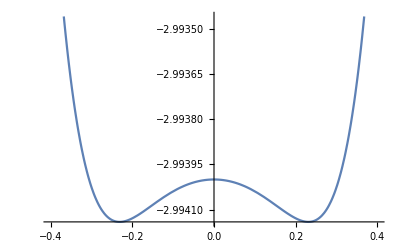
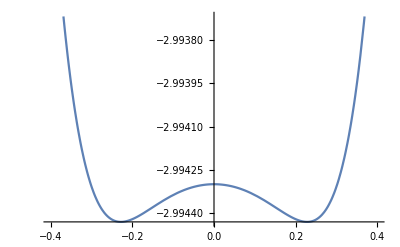
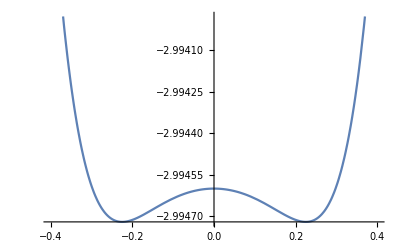
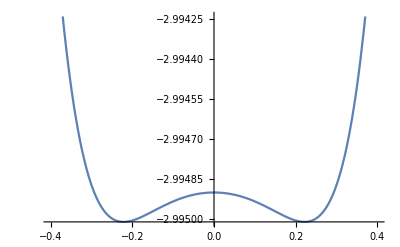
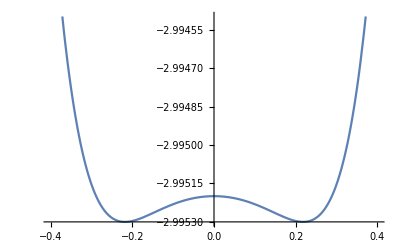
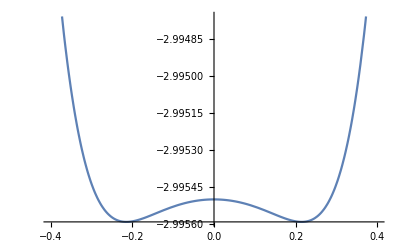
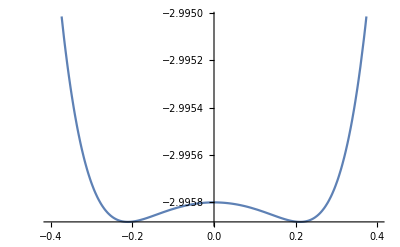
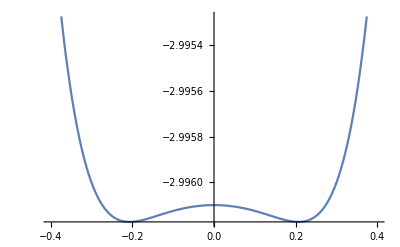

```mathematica
Table[Plot[{Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1]}+2 m^2,{m,-0.4,0.4}], {Δ,ds}](*3ladder rung - 2nd order*)
```

```mathematica
Series[{Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1]}+2 m^2,{m,0,8}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3& for some values of {Δ,m}.

{-3 Δ+(2-2/Δ) m^2+m^6/(2 Δ^5)-m^8/(2 Δ^7)+O[m]^9}

```mathematica
Eigenvalues[({{-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ}, {-Δ, -2 m, 0, -Δ, 0, -Δ, -Δ, 0}, {-Δ, 0, -2 m, -Δ, 0, -Δ, -Δ, 0}, {0, -Δ, -Δ, 2 m, -Δ, 0, 0, -Δ}, {-Δ, 0, 0, -Δ, -2 m, -Δ, -Δ, 0}, {0, -Δ, -Δ, 0, -Δ, 2 m, 0, -Δ}, {0, -Δ, -Δ, 0, -Δ, 0, 2 m, -Δ}, {-Δ, 0, 0, -Δ, 0, -Δ, -Δ, 6 m}})](*4ladder rung*)
```

{-2 m,-2 m,2 m,2 m,-2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4))}

```mathematica
Series[{-2 m,-2 m,2 m,2 m,-2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4))},{m,0,6}]
```

{-2 m+O[m]^7,-2 m+O[m]^7,2 m+O[m]^7,2 m+O[m]^7,-2 (√2 √(Δ^2-√(Δ^4)))-(√2 √(Δ^2-√(Δ^4)) (5-(√(Δ^4))/Δ^2) m^2)/(2 Δ^2-2 √(Δ^4))-(√(Δ^2-√(Δ^4)) (-15/(2 √(Δ^4) (2 Δ^2-2 √(Δ^4)))-((5-(√(Δ^4))/Δ^2)^2)/(2 (2 Δ^2-2 √(Δ^4))^2)) m^4)/(√2)-1/3 (√2 √(Δ^2-√(Δ^4)) ((45 √(Δ^4))/(8 Δ^6 (2 Δ^2-2 √(Δ^4)))-(3 (5-(√(Δ^4))/Δ^2) (-15/(2 √(Δ^4) (2 Δ^2-2 √(Δ^4)))-((5-(√(Δ^4))/Δ^2)^2)/(2 (2 Δ^2-2 √(Δ^4))^2)))/(4 (2 Δ^2-2 √(Δ^4))))) m^6+O[m]^7,2 √2 √(Δ^2-√(Δ^4))+(√2 √(Δ^2-√(Δ^4)) (5-(√(Δ^4))/Δ^2) m^2)/(2 Δ^2-2 √(Δ^4))+(√(Δ^2-√(Δ^4)) (-15/(2 √(Δ^4) (2 Δ^2-2 √(Δ^4)))-((5-(√(Δ^4))/Δ^2)^2)/(2 (2 Δ^2-2 √(Δ^4))^2)) m^4)/(√2)+1/3 √2 √(Δ^2-√(Δ^4)) ((45 √(Δ^4))/(8 Δ^6 (2 Δ^2-2 √(Δ^4)))-(3 (5-(√(Δ^4))/Δ^2) (-15/(2 √(Δ^4) (2 Δ^2-2 √(Δ^4)))-((5-(√(Δ^4))/Δ^2)^2)/(2 (2 Δ^2-2 √(Δ^4))^2)))/(4 (2 Δ^2-2 √(Δ^4)))) m^6+O[m]^7,-2 (√2 √(Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2) m^2)/(√2 √(Δ^2+√(Δ^4)))-(√(Δ^2+√(Δ^4)) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)) m^4)/(√2)-1/3 (√2 √(Δ^2+√(Δ^4)) (-(45 √(Δ^4))/(16 Δ^6 (Δ^2+√(Δ^4)))-(3 (5+(√(Δ^4))/Δ^2) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)))/(8 (Δ^2+√(Δ^4))))) m^6+O[m]^7,2 √2 √(Δ^2+√(Δ^4))+((5+(√(Δ^4))/Δ^2) m^2)/(√2 √(Δ^2+√(Δ^4)))+(√(Δ^2+√(Δ^4)) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)) m^4)/(√2)+1/3 √2 √(Δ^2+√(Δ^4)) (-(45 √(Δ^4))/(16 Δ^6 (Δ^2+√(Δ^4)))-(3 (5+(√(Δ^4))/Δ^2) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)))/(8 (Δ^2+√(Δ^4)))) m^6+O[m]^7}

```mathematica
ds=Range[0.99,1.1,.01];
```

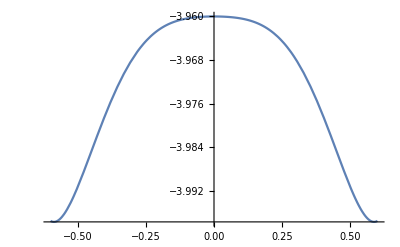
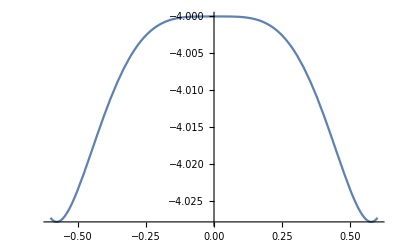
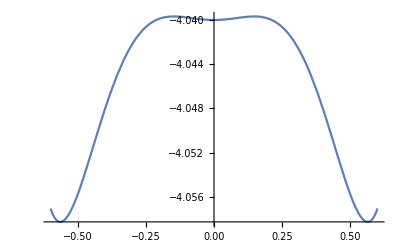
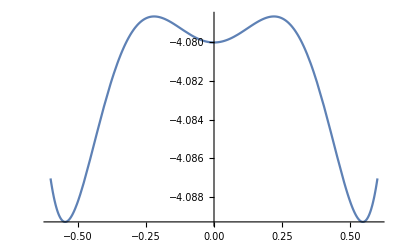
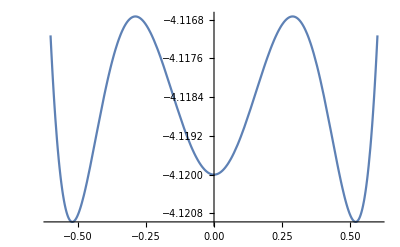
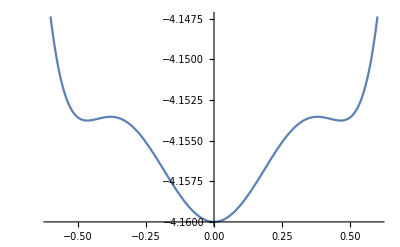
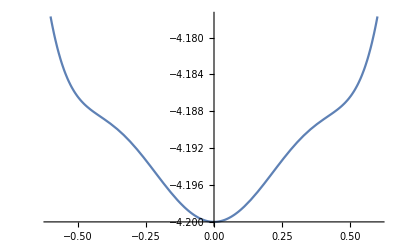
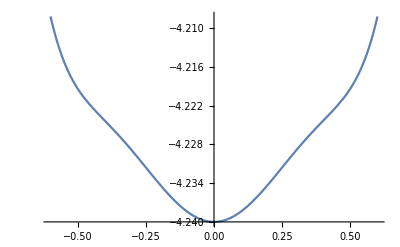

```mathematica
Table[Plot[3 m^2-2 (√2 √(Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2) m^2)/(√2 √(Δ^2+√(Δ^4)))-(√(Δ^2+√(Δ^4)) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)) m^4)/(√2)-1/3 (√2 √(Δ^2+√(Δ^4)) (-(45 √(Δ^4))/(16 Δ^6 (Δ^2+√(Δ^4)))-(3 (5+(√(Δ^4))/Δ^2) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)))/(8 (Δ^2+√(Δ^4))))) m^6,{m,-0.6,0.6}],{Δ,ds}](*4ladder rung - 1st order*)
```

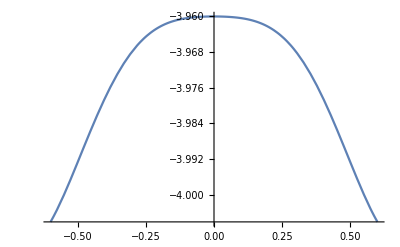
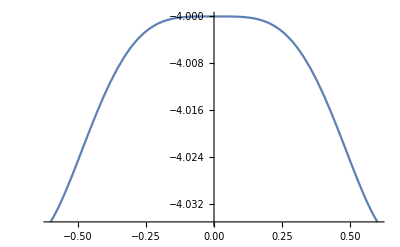
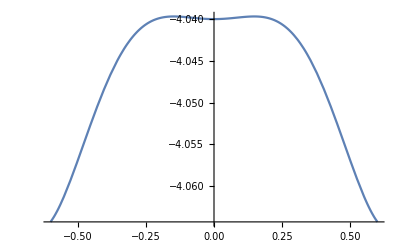
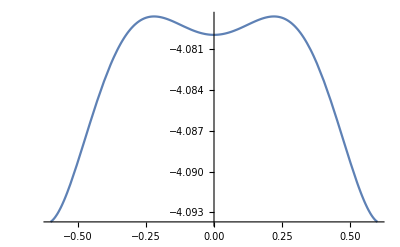
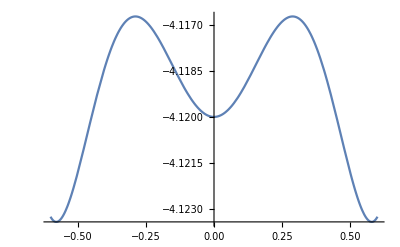
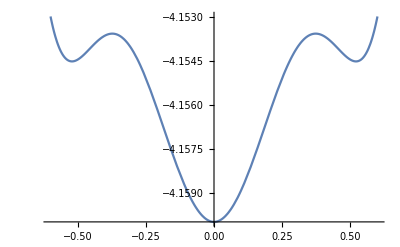
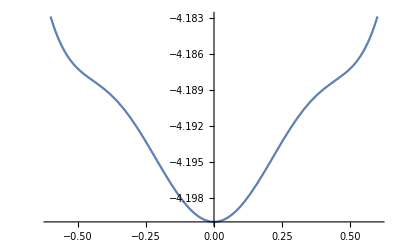
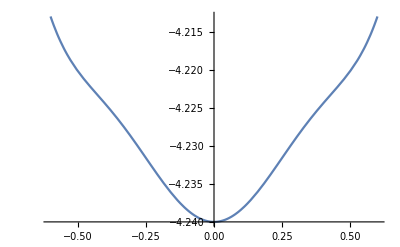

```mathematica
Table[Plot[3 m^2-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),{m,-0.6,0.6}],{Δ,ds}]
```

```mathematica
Series[{-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4))},{m,0,6}]
```

```mathematica
H=-2m (KroneckerProduct[z, I3] + KroneckerProduct[I3,z] + KroneckerProduct[I1,z,I2] +KroneckerProduct[I2,z,I1]) - Δ(KroneckerProduct[x,I3] + KroneckerProduct[I1,x,I2] + τ KroneckerProduct[x,x,x,x] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]) //MatrixForm
```

(-8 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ
-Δ | -4 m | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ τ | 0
-Δ | 0 | -4 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0
0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | 0
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ τ | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 4 m | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | -4 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | -Δ τ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | 0 | 0 | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
0 | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0
0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 4 m | 0 | -Δ
0 | -Δ τ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 4 m | -Δ
-Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 8 m)

```mathematica
Ham = Ham = H/. τ->1 //MatrixForm(*5ladder rung - 1st order*)
```

(-8 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | -4 m | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0
-Δ | 0 | -4 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0
0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 4 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -4 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0
0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 4 m | 0 | -Δ
0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 4 m | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 8 m)

```mathematica
eg = Eigenvalues[Ham]
```

```mathematica
Eigenvalues[({{-8 m, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, -4 m, 0, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, -Δ, 0}, {-Δ, 0, -4 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 0, 0}, {0, -Δ, -Δ, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, 0, 0}, {-Δ, 0, 0, 0, -4 m, -Δ, -Δ, 0, 0, 0, 0, -Δ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, 0, 0, -Δ, 0, -Δ, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, -Δ, -Δ, 4 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, -Δ, -4 m, -Δ, -Δ, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, -Δ, 0, -Δ, 0, 0, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ, 0, 0, 0, 0, -Δ, -Δ, 4 m, 0, 0, 0, -Δ}, {0, 0, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, -Δ, -Δ, 0}, {0, 0, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 4 m, 0, -Δ}, {0, -Δ, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, 0, 4 m, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, 8 m}})]
```

{-Δ,-Δ,Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,1],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,2],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,3],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,4],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,5]}

```mathematica
ds=Range[0.99,1.1,.01];
```

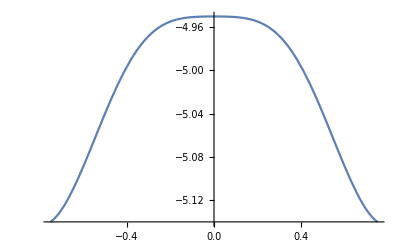
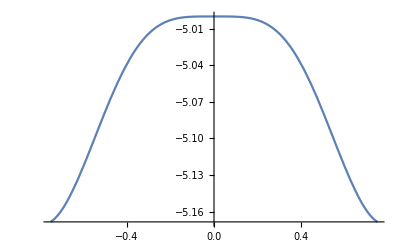
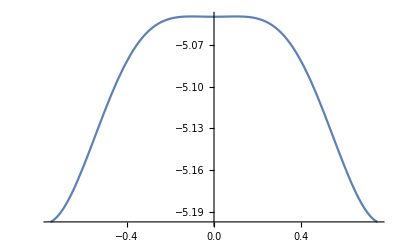
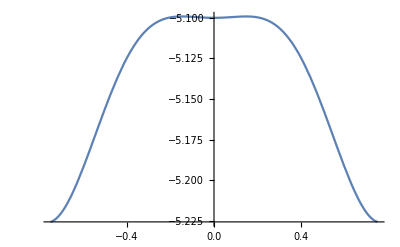
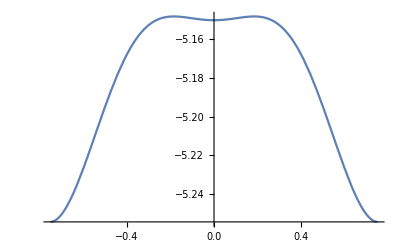
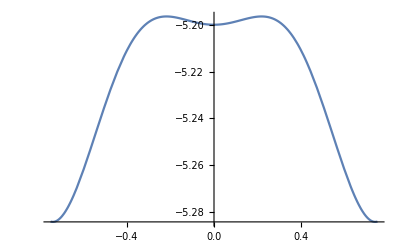
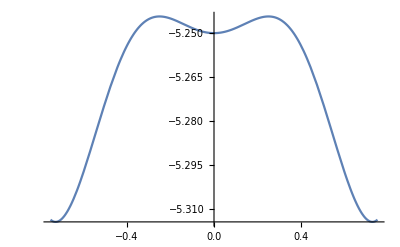
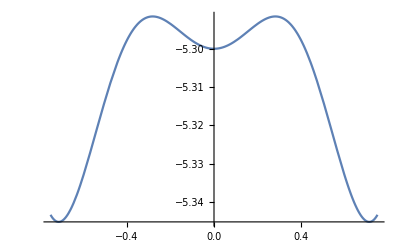

```mathematica
Table[Plot[{Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,1]}+4 m^2,{m,-0.75,0.75}], {Δ,ds}](*5ladder rung - 1st order*)
```

```mathematica
H=-2m (KroneckerProduct[I3,I2,z] + KroneckerProduct[I3,I1,z,I1] +KroneckerProduct[I3,z,I2]) - KroneckerProduct[z,I2,z,I2] - KroneckerProduct[I1,z,I2,z,I1] - KroneckerProduct[I2,z,I2,z]-Δ(KroneckerProduct[x,I3,I2] + KroneckerProduct[I1,x,I3,I1] + τ (KroneckerProduct[x,x,x,I3] + KroneckerProduct[I3,x,x,x]) + KroneckerProduct[I2,x,I3] + KroneckerProduct[I3,x,I2]+KroneckerProduct[I3,I1,x,I1]+KroneckerProduct[I3,I2,x]) //MatrixForm
```

(-3-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0
-Δ | 0 | -1-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0
0 | -Δ | -Δ | 1+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0
-Δ | 0 | 0 | -Δ τ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0
0 | -Δ | -Δ τ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0
0 | -Δ τ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0
-Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 3+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -3-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | -1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | 3+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -3-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | 3+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -1-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -3+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 3-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 3+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -3-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | -1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 3-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 1+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | -3+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 3-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -1-2 m | -Δ | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 1+2 m | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | -3+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ
0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0
0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ τ | -Δ | 0
0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ τ | 0 | 0 | -Δ
0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 1-2 m | -Δ | -Δ | 0
0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | -Δ | -1+2 m | 0 | -Δ
0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -3+6 m)

```mathematica
Ham = Ham = H/. τ->1 //MatrixForm
```

(-3-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
-Δ | 0 | -1-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | -Δ | -Δ | 1+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
-Δ | 0 | 0 | -Δ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | -Δ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | -Δ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
-Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 3+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -3-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | -1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | 3+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -3-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | 3+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -1-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -3+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 3-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 3+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -3-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | -1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 3-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 1+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | -3+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | 1+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 3-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | -1-2 m | -Δ | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 1+2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -1-2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | 1+2 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | -3+2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -1+6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 1-2 m | 0 | -Δ | 0 | -Δ | -Δ | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 1-2 m | -Δ | 0 | -Δ | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | -1+2 m | -Δ | 0 | 0 | -Δ
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 1-2 m | -Δ | -Δ | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | -Δ | -1+2 m | 0 | -Δ
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | -Δ | 0 | -Δ | 0 | -1+2 m | -Δ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | -3+6 m)

```mathematica
eg = Eigenvalues[Ham]
```

```mathematica
Eigenvalues[({{-3-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0}, {-Δ, -1-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0}, {-Δ, 0, -1-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0}, {0, -Δ, -Δ, 1+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0}, {-Δ, 0, 0, -Δ, -1-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, -Δ, 0, -Δ, 1+2 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0}, {0, -Δ, -Δ, 0, -Δ, 0, 1+2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0}, {-Δ, 0, 0, -Δ, 0, -Δ, -Δ, 3+6 m, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, 0, -1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, -3-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 1-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, -1+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 1-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, -Δ, -1+2 m, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -Δ, 0, -Δ, 0, 3+2 m, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, 1+6 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0}, {-Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 1-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, -3-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, -1+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, 1-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, -Δ, 3+2 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, -Δ, 0, -1+2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, 1+6 m, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, -1-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, -1-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, -3+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 3-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, -Δ, 1+2 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -Δ, 0, -Δ, 0, 1+2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, -1+6 m, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 1-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 1-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, 3+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, -3-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, -Δ, -1+2 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -Δ, 0, -Δ, 0, -1+2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, 1+6 m, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, -1-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 3-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, 1+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, -1-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, -Δ, -3+2 m, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -Δ, 0, -Δ, 0, 1+2 m, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, -1+6 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ}, {0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ, -Δ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 3-2 m, 0, -Δ, 0, -Δ, -Δ, 0, 0, -Δ, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, -1-2 m, -Δ, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 1+2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -1-2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, -Δ, 1+2 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, -Δ, 0, -3+2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, -1+6 m, 0, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 3-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ}, {0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 1-2 m, 0, -Δ, 0, -Δ, -Δ, 0}, {0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 1-2 m, -Δ, 0, -Δ, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, -1+2 m, -Δ, 0, 0, -Δ}, {0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 1-2 m, -Δ, -Δ, 0}, {0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, -Δ, -1+2 m, 0, -Δ}, {0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, -Δ, -Δ, 0, -Δ, 0, -1+2 m, -Δ}, {0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0, -Δ, -Δ, 0, 0, -Δ, 0, -Δ, -Δ, -3+6 m}})]
```

```mathematica
Eigenvalues[({{-4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -2-4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2+4 m, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 2-4 m, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2+4 m, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -4 m, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 4 m}})]
```

{-2,-2,2,2,0,0,0,0,2 (-1-2 m),2 (1-2 m),-4 m,-4 m,4 m,4 m,2 (-1+2 m),2 (1+2 m)}

```mathematica
Plot[Evaluate[Normal[{-2,-2,2,2,0,0,0,0,2 (-1-2 m),2 (1-2 m),-4 m,-4 m,4 m,4 m,2 (-1+2 m),2 (1+2 m)}+2 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[({{-4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -2-4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 2-4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -4 m, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 4 m, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2+4 m, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2+4 m, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 4 m}})]
```

{-2,-2,2,2,0,0,0,0,2 (-1-2 m),2 (1-2 m),-4 m,-4 m,4 m,4 m,2 (-1+2 m),2 (1+2 m)}

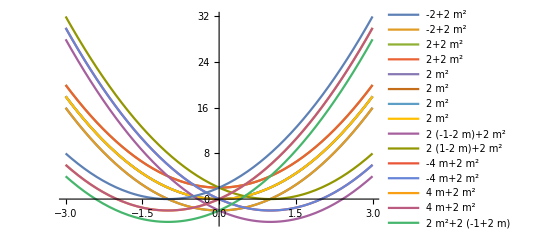

```mathematica
Plot[Evaluate[Normal[{-2,-2,2,2,0,0,0,0,2 (-1-2 m),2 (1-2 m),-4 m,-4 m,4 m,4 m,2 (-1+2 m),2 (1+2 m)}+2 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
eg1 = Eigenvalues[Ham]/.{ Δ->0.5}
```

```mathematica
Eigenvalues[({{-4 m, -0.5, -0.5, -0.5, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0}, {-0.5, -2, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0}, {-0.5, -0.5, 2, -0.5, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0}, {-0.5, -0.5, -0.5, 4 m, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, -2-4 m, -0.5, -0.5, -0.5, -0.5, 0, 0, 0, -0.5, 0, 0, 0}, {0, -0.5, 0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5, 0, 0}, {0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0, -0.5, 0, 0, 0, -0.5, 0}, {0, 0, 0, -0.5, -0.5, -0.5, -0.5, 2+4 m, 0, 0, 0, -0.5, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, -0.5, 0, 0, 0, 2-4 m, -0.5, -0.5, -0.5, -0.5, 0, 0, 0}, {0, -0.5, 0, 0, 0, -0.5, 0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0}, {0, 0, -0.5, 0, 0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0, -0.5, 0}, {0, 0, 0, -0.5, 0, 0, 0, -0.5, -0.5, -0.5, -0.5, -2+4 m, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -4 m, -0.5, -0.5, -0.5}, {0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, -0.5, 2, -0.5, -0.5}, {0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, -0.5, -0.5, -2, -0.5}, {0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, -0.5, -0.5, -0.5, 4 m}})]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Eigenvalues[{{-4 m,-0.5,-0.5,-0.5,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,0},{-0.5,-2,-0.5,-0.5,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0},{-0.5,-0.5,2,-0.5,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0},{-0.5,-0.5,-0.5,4 m,0,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5},{-0.5,0,0,0,-2-4 m,-0.5,-0.5,-0.5,-0.5,0,0,0,-0.5,0,0,0},{0,-0.5,0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0,0,-0.5,0,0},{0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0,-0.5,0,0,0,-0.5,0},{0,0,0,-0.5,-0.5,-0.5,-0.5,2+4 m,0,0,0,-0.5,0,0,0,-0.5},{-0.5,0,0,0,-0.5,0,0,0,2-4 m,-0.5,-0.5,-0.5,-0.5,0,0,0},{0,-0.5,0,0,0,-0.5,0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0},{0,0,-0.5,0,0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0,-0.5,0},{0,0,0,-0.5,0,0,0,-0.5,-0.5,-0.5,-0.5,-2+4 m,0,0,0,-0.5},{-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,0,-4 m,-0.5,-0.5,-0.5},{0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,-0.5,2,-0.5,-0.5},{0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,-0.5,-0.5,-2,-0.5},{0,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,-0.5,-0.5,-0.5,4 m}}]

```mathematica
eg1 = Eigenvalues[Ham]/.{ Δ->1}
```

```mathematica
Eigenvalues[({{-4 m, -1, -1, -1, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0}, {-1, -2, -1, -1, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0}, {-1, -1, 2, -1, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0}, {-1, -1, -1, 4 m, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1}, {-1, 0, 0, 0, -2-4 m, -1, -1, -1, -1, 0, 0, 0, -1, 0, 0, 0}, {0, -1, 0, 0, -1, 0, -1, -1, 0, -1, 0, 0, 0, -1, 0, 0}, {0, 0, -1, 0, -1, -1, 0, -1, 0, 0, -1, 0, 0, 0, -1, 0}, {0, 0, 0, -1, -1, -1, -1, 2+4 m, 0, 0, 0, -1, 0, 0, 0, -1}, {-1, 0, 0, 0, -1, 0, 0, 0, 2-4 m, -1, -1, -1, -1, 0, 0, 0}, {0, -1, 0, 0, 0, -1, 0, 0, -1, 0, -1, -1, 0, -1, 0, 0}, {0, 0, -1, 0, 0, 0, -1, 0, -1, -1, 0, -1, 0, 0, -1, 0}, {0, 0, 0, -1, 0, 0, 0, -1, -1, -1, -1, -2+4 m, 0, 0, 0, -1}, {-1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -4 m, -1, -1, -1}, {0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1, 2, -1, -1}, {0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, -1, -1, -2, -1}, {0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, -1, -1, -1, 4 m}})]
```

{2,Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,1],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,2],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,3],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,4],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,5],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,1],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,2],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,3],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,4],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,5],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,6],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,7],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,8],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,9],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,10]}

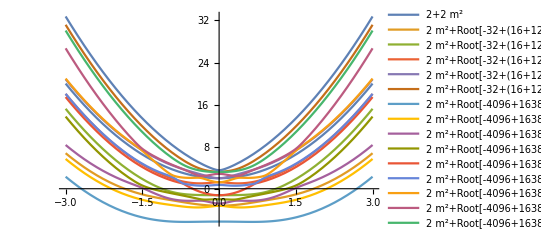

```mathematica
Plot[Evaluate[Normal[{2,Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,1],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,2],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,3],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,4],Root[-32+(16+128 m^2) #1+24 #1^2+(-12-16 m^2) #1^3-2 #1^4+#1^5&,5],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,1],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,2],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,3],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,4],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,5],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,6],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,7],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,8],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,9],Root[-4096+16384 m^2-16384 m^4+(4096+16384 m^2-65536 m^4+32768 m^6) #1+(6144+14336 m^2-16384 m^4+49152 m^6) #1^2+(-4096-6144 m^2-4096 m^4-8192 m^6) #1^3+(-3008-5120 m^2-7168 m^4-4096 m^6) #1^4+(1088+1792 m^2+2048 m^4) #1^5+(544+896 m^2+768 m^4) #1^6+(-112-160 m^2) #1^7+(-40-48 m^2) #1^8+4 #1^9+#1^10&,10]}+2 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[({{-4 m, -1, -1, -1, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0}, {-1, -2, -1, -1, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0}, {-1, -1, -2-4 m, -1, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0}, {-1, -1, -1, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1}, {-1, 0, 0, 0, 2-4 m, -1, -1, -1, -1, 0, 0, 0, -1, 0, 0, 0}, {0, -1, 0, 0, -1, 0, -1, -1, 0, -1, 0, 0, 0, -1, 0, 0}, {0, 0, -1, 0, -1, -1, -4 m, -1, 0, 0, -1, 0, 0, 0, -1, 0}, {0, 0, 0, -1, -1, -1, -1, 2, 0, 0, 0, -1, 0, 0, 0, -1}, {-1, 0, 0, 0, -1, 0, 0, 0, 2, -1, -1, -1, -1, 0, 0, 0}, {0, -1, 0, 0, 0, -1, 0, 0, -1, 4 m, -1, -1, 0, -1, 0, 0}, {0, 0, -1, 0, 0, 0, -1, 0, -1, -1, 0, -1, 0, 0, -1, 0}, {0, 0, 0, -1, 0, 0, 0, -1, -1, -1, -1, 2+4 m, 0, 0, 0, -1}, {-1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, 0, -1, -1, -1}, {0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1, -2+4 m, -1, -1}, {0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, 0, -1, -1, -2, -1}, {0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 0, -1, -1, -1, -1, 4 m}})]
```

{-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,1],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,2],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,3],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,4]}

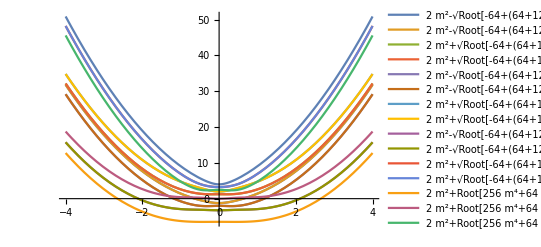

```mathematica
Plot[Evaluate[Normal[{-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,1],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,2],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],-√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],√Root[-64+(64+128 m^2) #1+(-16-16 m^2) #1^2+#1^3&,3],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,1],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,2],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,3],Root[256 m^4+64 #1+(-32-32 m^2) #1^2+#1^4&,4]}+2 m^2]],{m, -4,4}, PlotLegends->"Expressions"]
```

```mathematica
eg3 = Eigenvalues[Ham]/.{ Δ->2}
```

```mathematica
Eigenvalues[({{-4 m, -2, -2, -2, -2, 0, 0, 0, -2, 0, 0, 0, -2, 0, 0, 0}, {-2, -2, -2, -2, 0, -2, 0, 0, 0, -2, 0, 0, 0, -2, 0, 0}, {-2, -2, -2-4 m, -2, 0, 0, -2, 0, 0, 0, -2, 0, 0, 0, -2, 0}, {-2, -2, -2, 0, 0, 0, 0, -2, 0, 0, 0, -2, 0, 0, 0, -2}, {-2, 0, 0, 0, 2-4 m, -2, -2, -2, -2, 0, 0, 0, -2, 0, 0, 0}, {0, -2, 0, 0, -2, 0, -2, -2, 0, -2, 0, 0, 0, -2, 0, 0}, {0, 0, -2, 0, -2, -2, -4 m, -2, 0, 0, -2, 0, 0, 0, -2, 0}, {0, 0, 0, -2, -2, -2, -2, 2, 0, 0, 0, -2, 0, 0, 0, -2}, {-2, 0, 0, 0, -2, 0, 0, 0, 2, -2, -2, -2, -2, 0, 0, 0}, {0, -2, 0, 0, 0, -2, 0, 0, -2, 4 m, -2, -2, 0, -2, 0, 0}, {0, 0, -2, 0, 0, 0, -2, 0, -2, -2, 0, -2, 0, 0, -2, 0}, {0, 0, 0, -2, 0, 0, 0, -2, -2, -2, -2, 2+4 m, 0, 0, 0, -2}, {-2, 0, 0, 0, -2, 0, 0, 0, -2, 0, 0, 0, 0, -2, -2, -2}, {0, -2, 0, 0, 0, -2, 0, 0, 0, -2, 0, 0, -2, -2+4 m, -2, -2}, {0, 0, -2, 0, 0, 0, -2, 0, 0, 0, -2, 0, -2, -2, -2, -2}, {0, 0, 0, -2, 0, 0, 0, -2, 0, 0, 0, -2, -2, -2, -2, 4 m}})]
```

{-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,1],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,2],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,3],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,4]}

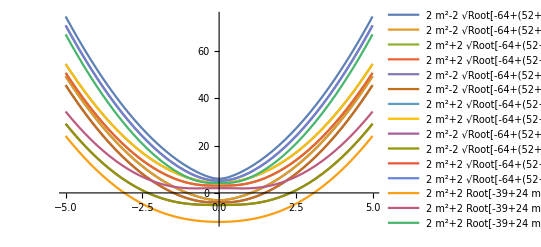

```mathematica
Plot[Evaluate[Normal[{-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,1],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,2],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],-2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 √Root[-64+(52+20 m^2) #1+(-13-4 m^2) #1^2+#1^3&,3],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,1],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,2],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,3],2 Root[-39+24 m^2+16 m^4+64 #1+(-26-8 m^2) #1^2+#1^4&,4]}+ 2 m^2]],{m,-5,5}, PlotLegends->"Expressions"]
```

```mathematica
eg3 = Eigenvalues[Ham]/.{ Δ->3}
```

Eigenvalues[(-4 m | -3 | -3 | -3 τ | -3 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 τ | 0 | 0 | 0
-3 | -2 | -3 τ | -3 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 τ | 0 | 0
-3 | -3 τ | -2-4 m | -3 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 τ | 0
-3 τ | -3 | -3 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 τ
-3 | 0 | 0 | 0 | 2-4 m | -3 | -3 | -3 τ | -3 τ | 0 | 0 | 0 | -3 | 0 | 0 | 0
0 | -3 | 0 | 0 | -3 | 0 | -3 τ | -3 | 0 | -3 τ | 0 | 0 | 0 | -3 | 0 | 0
0 | 0 | -3 | 0 | -3 | -3 τ | -4 m | -3 | 0 | 0 | -3 τ | 0 | 0 | 0 | -3 | 0
0 | 0 | 0 | -3 | -3 τ | -3 | -3 | 2 | 0 | 0 | 0 | -3 τ | 0 | 0 | 0 | -3
-3 | 0 | 0 | 0 | -3 τ | 0 | 0 | 0 | 2 | -3 | -3 | -3 τ | -3 | 0 | 0 | 0
0 | -3 | 0 | 0 | 0 | -3 τ | 0 | 0 | -3 | 4 m | -3 τ | -3 | 0 | -3 | 0 | 0
0 | 0 | -3 | 0 | 0 | 0 | -3 τ | 0 | -3 | -3 τ | 0 | -3 | 0 | 0 | -3 | 0
0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 τ | -3 τ | -3 | -3 | 2+4 m | 0 | 0 | 0 | -3
-3 τ | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0 | -3 | -3 | -3 τ
0 | -3 τ | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | 0 | -3 | -2+4 m | -3 τ | -3
0 | 0 | -3 τ | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 0 | -3 | -3 τ | -2 | -3
0 | 0 | 0 | -3 τ | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | -3 τ | -3 | -3 | 4 m)]

```mathematica
Eigenvalues[({{-4 m, -3, -3, -3, -3, 0, 0, 0, -3, 0, 0, 0, -3, 0, 0, 0}, {-3, -2, -3, -3, 0, -3, 0, 0, 0, -3, 0, 0, 0, -3, 0, 0}, {-3, -3, -2-4 m, -3, 0, 0, -3, 0, 0, 0, -3, 0, 0, 0, -3, 0}, {-3, -3, -3, 0, 0, 0, 0, -3, 0, 0, 0, -3, 0, 0, 0, -3}, {-3, 0, 0, 0, 2-4 m, -3, -3, -3, -3, 0, 0, 0, -3, 0, 0, 0}, {0, -3, 0, 0, -3, 0, -3, -3, 0, -3, 0, 0, 0, -3, 0, 0}, {0, 0, -3, 0, -3, -3, -4 m, -3, 0, 0, -3, 0, 0, 0, -3, 0}, {0, 0, 0, -3, -3, -3, -3, 2, 0, 0, 0, -3, 0, 0, 0, -3}, {-3, 0, 0, 0, -3, 0, 0, 0, 2, -3, -3, -3, -3, 0, 0, 0}, {0, -3, 0, 0, 0, -3, 0, 0, -3, 4 m, -3, -3, 0, -3, 0, 0}, {0, 0, -3, 0, 0, 0, -3, 0, -3, -3, 0, -3, 0, 0, -3, 0}, {0, 0, 0, -3, 0, 0, 0, -3, -3, -3, -3, 2+4 m, 0, 0, 0, -3}, {-3, 0, 0, 0, -3, 0, 0, 0, -3, 0, 0, 0, 0, -3, -3, -3}, {0, -3, 0, 0, 0, -3, 0, 0, 0, -3, 0, 0, -3, -2+4 m, -3, -3}, {0, 0, -3, 0, 0, 0, -3, 0, 0, 0, -3, 0, -3, -3, -2, -3}, {0, 0, 0, -3, 0, 0, 0, -3, 0, 0, 0, -3, -3, -3, -3, 4 m}})]
```

{-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,1],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,2],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,3],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,4]}

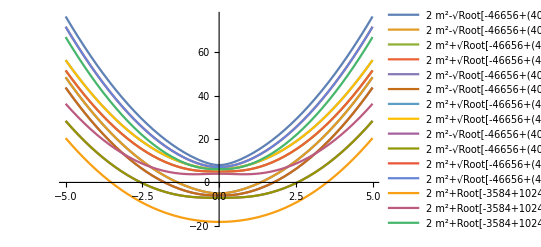

```mathematica
Plot[Evaluate[Normal[{-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,1],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,2],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],-√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],√Root[-46656+(4032+640 m^2) #1+(-112-16 m^2) #1^2+#1^3&,3],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,1],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,2],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,3],Root[-3584+1024 m^2+256 m^4+1728 #1+(-224-32 m^2) #1^2+#1^4&,4]}+2 m^2]],{m,-5,5}, PlotLegends->"Expressions"]
```

```mathematica
eg5 = Eigenvalues[Ham]/.{ Δ->10}
```

```mathematica
Eigenvalues[({{-4 m, -10, -10, -10, -10, 0, 0, 0, -10, 0, 0, 0, -10, 0, 0, 0}, {-10, -2, -10, -10, 0, -10, 0, 0, 0, -10, 0, 0, 0, -10, 0, 0}, {-10, -10, -2-4 m, -10, 0, 0, -10, 0, 0, 0, -10, 0, 0, 0, -10, 0}, {-10, -10, -10, 0, 0, 0, 0, -10, 0, 0, 0, -10, 0, 0, 0, -10}, {-10, 0, 0, 0, 2-4 m, -10, -10, -10, -10, 0, 0, 0, -10, 0, 0, 0}, {0, -10, 0, 0, -10, 0, -10, -10, 0, -10, 0, 0, 0, -10, 0, 0}, {0, 0, -10, 0, -10, -10, -4 m, -10, 0, 0, -10, 0, 0, 0, -10, 0}, {0, 0, 0, -10, -10, -10, -10, 2, 0, 0, 0, -10, 0, 0, 0, -10}, {-10, 0, 0, 0, -10, 0, 0, 0, 2, -10, -10, -10, -10, 0, 0, 0}, {0, -10, 0, 0, 0, -10, 0, 0, -10, 4 m, -10, -10, 0, -10, 0, 0}, {0, 0, -10, 0, 0, 0, -10, 0, -10, -10, 0, -10, 0, 0, -10, 0}, {0, 0, 0, -10, 0, 0, 0, -10, -10, -10, -10, 2+4 m, 0, 0, 0, -10}, {-10, 0, 0, 0, -10, 0, 0, 0, -10, 0, 0, 0, 0, -10, -10, -10}, {0, -10, 0, 0, 0, -10, 0, 0, 0, -10, 0, 0, -10, -2+4 m, -10, -10}, {0, 0, -10, 0, 0, 0, -10, 0, 0, 0, -10, 0, -10, -10, -2, -10}, {0, 0, 0, -10, 0, 0, 0, -10, 0, 0, 0, -10, -10, -10, -10, 4 m}})]
```

{-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,1],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,2],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,3],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,4]}

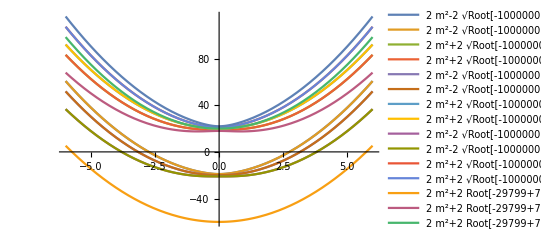

```mathematica
Plot[Evaluate[Normal[{-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,1],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,2],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],-2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 √Root[-1000000+(30100+404 m^2) #1+(-301-4 m^2) #1^2+#1^3&,3],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,1],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,2],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,3],2 Root[-29799+792 m^2+16 m^4+8000 #1+(-602-8 m^2) #1^2+#1^4&,4]}+2 m^2]],{m,-6,6}, PlotLegends->"Expressions"]
```

```mathematica
eg6 = Eigenvalues[Ham]/.{ Δ->0.5}
```

```mathematica
Eigenvalues[({{-4 m, -0.5, -0.5, -0.5, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0}, {-0.5, -2, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0}, {-0.5, -0.5, -2-4 m, -0.5, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0}, {-0.5, -0.5, -0.5, 0, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, 2-4 m, -0.5, -0.5, -0.5, -0.5, 0, 0, 0, -0.5, 0, 0, 0}, {0, -0.5, 0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0, 0, -0.5, 0, 0}, {0, 0, -0.5, 0, -0.5, -0.5, -4 m, -0.5, 0, 0, -0.5, 0, 0, 0, -0.5, 0}, {0, 0, 0, -0.5, -0.5, -0.5, -0.5, 2, 0, 0, 0, -0.5, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, -0.5, 0, 0, 0, 2, -0.5, -0.5, -0.5, -0.5, 0, 0, 0}, {0, -0.5, 0, 0, 0, -0.5, 0, 0, -0.5, 4 m, -0.5, -0.5, 0, -0.5, 0, 0}, {0, 0, -0.5, 0, 0, 0, -0.5, 0, -0.5, -0.5, 0, -0.5, 0, 0, -0.5, 0}, {0, 0, 0, -0.5, 0, 0, 0, -0.5, -0.5, -0.5, -0.5, 2+4 m, 0, 0, 0, -0.5}, {-0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, 0, -0.5, -0.5, -0.5}, {0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, -0.5, -2+4 m, -0.5, -0.5}, {0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, -0.5, -0.5, -2, -0.5}, {0, 0, 0, -0.5, 0, 0, 0, -0.5, 0, 0, 0, -0.5, -0.5, -0.5, -0.5, 4 m}})]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Eigenvalues[{{-4 m,-0.5,-0.5,-0.5,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,0},{-0.5,-2,-0.5,-0.5,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0},{-0.5,-0.5,-2-4 m,-0.5,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0},{-0.5,-0.5,-0.5,0,0,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5},{-0.5,0,0,0,2-4 m,-0.5,-0.5,-0.5,-0.5,0,0,0,-0.5,0,0,0},{0,-0.5,0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0,0,-0.5,0,0},{0,0,-0.5,0,-0.5,-0.5,-4 m,-0.5,0,0,-0.5,0,0,0,-0.5,0},{0,0,0,-0.5,-0.5,-0.5,-0.5,2,0,0,0,-0.5,0,0,0,-0.5},{-0.5,0,0,0,-0.5,0,0,0,2,-0.5,-0.5,-0.5,-0.5,0,0,0},{0,-0.5,0,0,0,-0.5,0,0,-0.5,4 m,-0.5,-0.5,0,-0.5,0,0},{0,0,-0.5,0,0,0,-0.5,0,-0.5,-0.5,0,-0.5,0,0,-0.5,0},{0,0,0,-0.5,0,0,0,-0.5,-0.5,-0.5,-0.5,2+4 m,0,0,0,-0.5},{-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,0,0,-0.5,-0.5,-0.5},{0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,0,-0.5,-2+4 m,-0.5,-0.5},{0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,0,-0.5,-0.5,-2,-0.5},{0,0,0,-0.5,0,0,0,-0.5,0,0,0,-0.5,-0.5,-0.5,-0.5,4 m}}]